## Introduction

Code to simulate the 1D swarmalator model (see [1] below) with local coupling. 

References:
[1] Sync and swarm: solvable model of non-identical swarmalators:  https://arxiv.org/abs/2203.10191

## Main

### Animation -- plot results as they are being generted

The code is fast for σ=2π, but slow for σ<2π. I must figure out a way to speed it up.

$Aborted

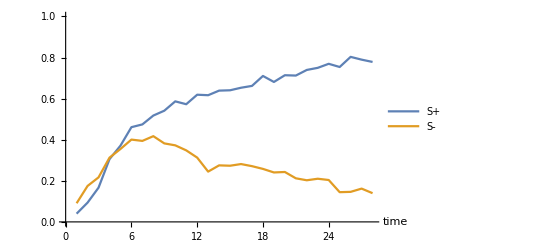

```mathematica
{dt,n1,T}={0.25,100,100};  (*dt = timestep, n = number of swarmalators*)
{J,k,γ,σ}={5,-0.1,0.25,π};   
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n1}],ConstantArray[0,{2,n1}]};
omega=RandomVariate[CauchyDistribution[0,γ],n1];
nu=RandomVariate[CauchyDistribution[0,γ],n1];
results={};
{Wps,Wms}={{},{}};
Dynamic[results]
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,omega,nu,σ];
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
z0=znew;t++;
{Wp,Wm}=findWs[znew];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
results=plotResults[znew]
];
ListPlot[{Wps,Wms}//Abs,Joined->True,PlotRange->{0,1},AxesLabel->{Style["time",15]},PlotLegends->{Style["S+",15],Style["S-",13]}]
```

## Make scatter plots

### Make data

#### σ = 2 π

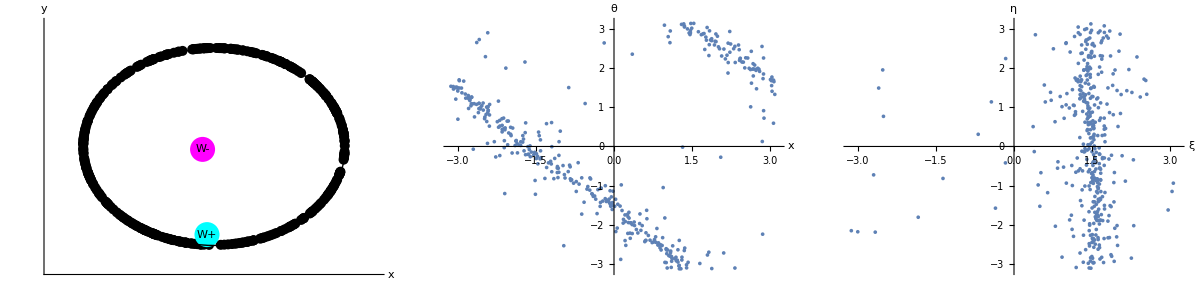

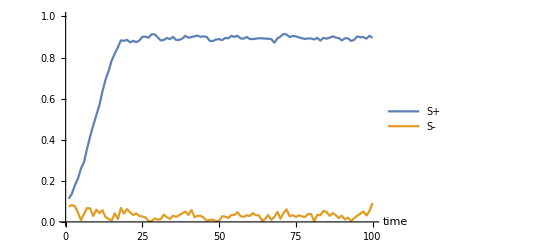

```mathematica
{J,k,Δ,σ}={5,-3,0.05,2π};   
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n1}],ConstantArray[0,{2,n1}]};
omega=RandomVariate[CauchyDistribution[0,Δ],n1];
nu=RandomVariate[CauchyDistribution[0,Δ],n1];
results={};
{Wps,Wms}={{},{}};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,omega,nu,σ];
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
z0=znew;t++;
{Wp,Wm}=findWs[znew];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
z00=znew;
plotResults[znew]
ListPlot[{Wps,Wms}//Abs,Joined->True,PlotRange->{0,1},AxesLabel->{Style["time",15]},PlotLegends->{Style["S+",15],Style["S-",13]}]
```

#### σ = 0.5 π

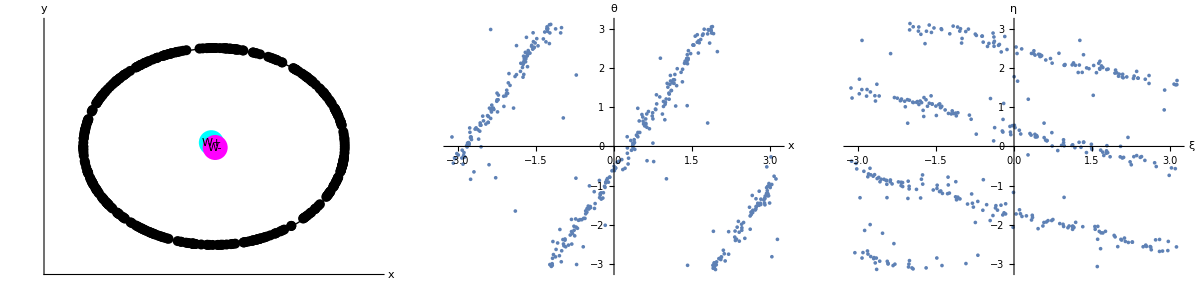

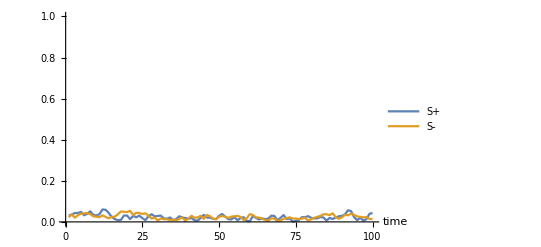

```mathematica
{J,k,Δ,σ}={5,-3,0.05,0.5π};   
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n1}],ConstantArray[0,{2,n1}]};
omega=RandomVariate[CauchyDistribution[0,Δ],n1];
nu=RandomVariate[CauchyDistribution[0,Δ],n1];
results={};
{Wps,Wms}={{},{}};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,omega,nu,σ];
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
z0=znew;t++;
{Wp,Wm}=findWs[znew];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
z1=znew;
plotResults[znew]
ListPlot[{Wps,Wms}//Abs,Joined->True,PlotRange->{0,1},AxesLabel->{Style["time",15]},PlotLegends->{Style["S+",15],Style["S-",13]}]
```

#### σ = 0.25 π

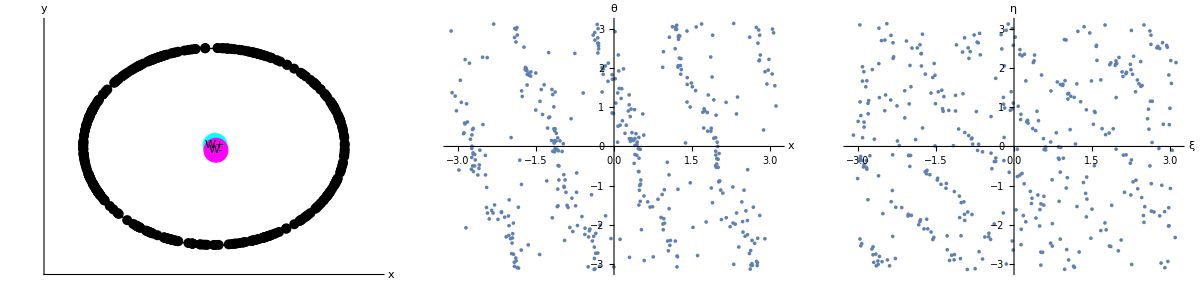

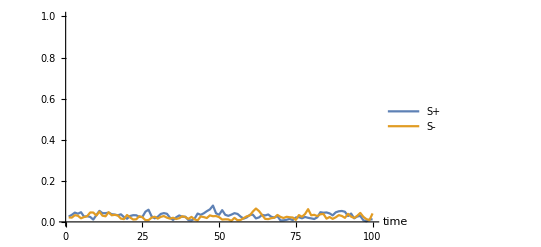

```mathematica
{J,k,Δ,σ}={5,-3,0.05,0.25π};   
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n1}],ConstantArray[0,{2,n1}]};
omega=RandomVariate[CauchyDistribution[0,Δ],n1];
nu=RandomVariate[CauchyDistribution[0,Δ],n1];
results={};
{Wps,Wms}={{},{}};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,omega,nu,σ];
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
z0=znew;t++;
{Wp,Wm}=findWs[znew];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
plotResults[znew]
z2=znew;
ListPlot[{Wps,Wms}//Abs,Joined->True,PlotRange->{0,1},AxesLabel->{Style["time",15]},PlotLegends->{Style["S+",15],Style["S-",13]}]
```

#### σ = 0.1 π

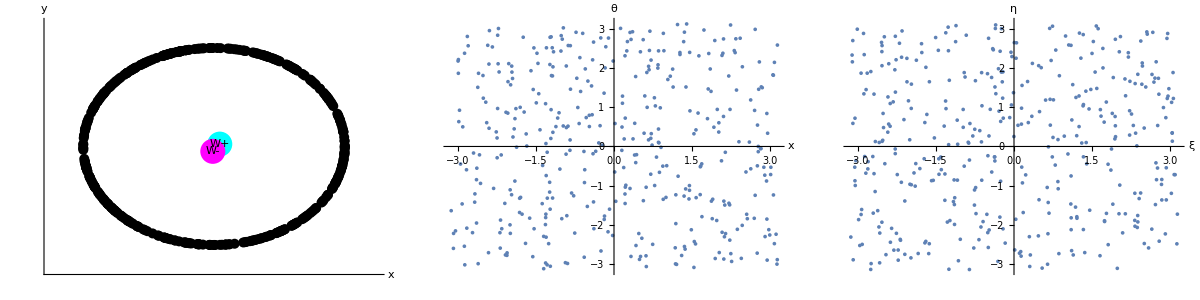

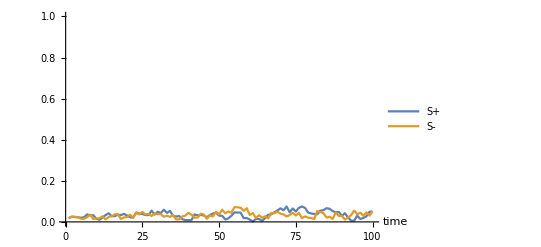

```mathematica
{J,k,Δ,σ}={5,-3,0.05,0.1π};   
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n1}],ConstantArray[0,{2,n1}]};
omega=RandomVariate[CauchyDistribution[0,Δ],n1];
nu=RandomVariate[CauchyDistribution[0,Δ],n1];
results={};
{Wps,Wms}={{},{}};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,omega,nu,σ];
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
z0=znew;t++;
{Wp,Wm}=findWs[znew];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
z3=znew;
plotResults[znew]
ListPlot[{Wps,Wms}//Abs,Joined->True,PlotRange->{0,1},AxesLabel->{Style["time",15]},PlotLegends->{Style["S+",15],Style["S-",13]}]
```

### Plot together

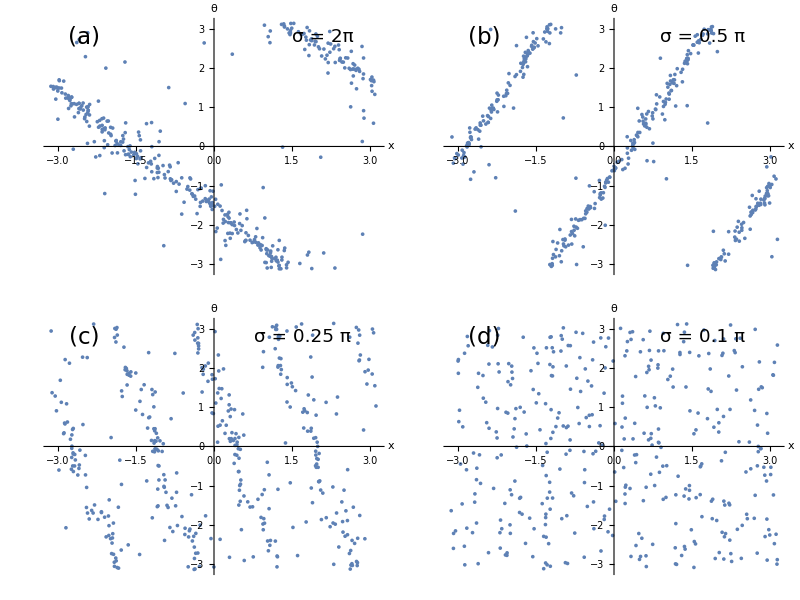

```mathematica
insetSize=23;
letterSize=20;
p0=ListPlot[{z00[[1,All]]//mod,z00[[2,All]]//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesStyle->17,AxesLabel->{Style["x",letterSize],Style["θ",letterSize]},Epilog->{Text[Style["(a)",insetSize],{-2.5,2.8}],Text[Style["σ = 2π",0.8insetSize],{2.1,2.8}]}];
p1=ListPlot[{z1[[1,All]]//mod,z1[[2,All]]//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesStyle->17,AxesLabel->{Style["x",letterSize],Style["θ",letterSize]},Epilog->{Text[Style["(b)",insetSize],{-2.5,2.8}],Text[Style["σ = 0.5 π",0.8insetSize],{1.7,2.8}]}];
p2=ListPlot[{z2[[1,All]]//mod,z2[[2,All]]//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesStyle->17,AxesLabel->{Style["x",letterSize],Style["θ",letterSize]},Epilog->{Text[Style["(c)",insetSize],{-2.5,2.8}],Text[Style["σ = 0.25 π",0.8insetSize],{1.7,2.8}]}];
p3=ListPlot[{z3[[1,All]]//mod,z3[[2,All]]//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesStyle->17,AxesLabel->{Style["x",letterSize],Style["θ",letterSize]},Epilog->{Text[Style["(d)",insetSize],{-2.5,2.8}],Text[Style["σ = 0.1 π",0.8insetSize],{1.7,2.8}]}];
pAll=Grid[{{p0,p1},{p2,p3}}]
SetDirectory[NotebookDirectory[]];
Export["figures/phase-waves-local-coupling-geodesic.png",pAll];
```

## Functions

```mathematica
(*Geodesic distance*)
dist[x1_,x2_]:=Compile[{{x1,_Real},{x2,_Real}},
Return[Min[{Abs[Mod[x2,2π]-Mod[x1,2π]],Abs[2π-(Mod[x2,2π]-Mod[x1,2π])],Abs[-2π-(Mod[x2,2π]-Mod[x1,2π])]}]]
];

rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{k,_Real},{omega,_Real,1},{nu,_Real,1},{σ,_Real}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,xj,xi,rep,A,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
{xj,xi}={z[[1,j]],z[[1,i]]};
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
If[σ>=2π,
(*If global coupling, speed up by not calculating dist*)
xtemp=J*Sin[xji] Cos[thetaji];
thetatemp=k*Sin[thetaji] Cos[xji],
(*Else calculate dist*)
xtemp=J*Sin[xji] Cos[thetaji]HeavisideTheta[σ-dist1[xi,xj]];
thetatemp=k*Sin[thetaji] Cos[xji]HeavisideTheta[σ-dist1[xi,xj]];
];
vel[[1,i]]+=xtemp;vel[[1,j]]+=-xtemp;
vel[[2,i]]+=thetatemp;vel[[2,j]]+=-thetatemp;
];
vel[[1,i]]=nu[[i]]+vel[[1,i]]/n;
vel[[2,i]]=omega[[i]]+vel[[2,i]]/n;
];
vel
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
]

plotResults[z_]:=Block[{colors,Wp,Wm,p1,p2,p3},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[2,All]],2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];
p1=Graphics[{

(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],
Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],
Black,Circle[{0,0},1]

},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];
p2=ListPlot[{z[[1,All]]//mod,z[[2,All]]//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];
p3=ListPlot[{z[[1,All]]+z[[2,All]],z[[1,All]]-z[[2,All]]}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];
Return[Grid[{{p1,p2,p3}}]
]
];

plotResults1DB[z_]:=Block[{colors},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[2,All]],2π]-1)/(2π)+380);
Return[ListPlot[{z[[1,All]],z[[2,All]]}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium]]
];


rk4[z_,F_,dt_,J_,k_,omega_,nu_,σ_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k,omega,nu,σ];
k2=F[z+dt/2 k1,n,J,k,omega,nu,σ];
k3=F[z+dt/2 k2,n,J,k,omega,nu,σ];
k4=F[z+dt k3,n,J,k,omega,nu,σ];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findMeanV[znew_,z_,dt_]:=Block[{v},
v=(znew-z)/dt;
v=(v[[1,All]]^2+v[[2,All]]^2)^(1/2);
Return[Mean[v]]
];

findGamma[xs_,θs_,cutoff_]:=Block[{gammas,i,n,x,θ,xSteady,rangeSteadyX,gammaX,θSteady,rangeSteadyθ,gammaθ,index},
(*Find fraction of swarmalators that have completed at least 
 one full oscillation (0,2π) mod 2π, after transients have been discarded *)

n= Dimensions[xs][[2]];
gammas={};
For[i=1,i≤n,i++,
{x,θ}={xs[[All,i]],θs[[All,i]]};

(*Check for one loop when x has approximately achieved its steady state*)
xSteady=x[[cutoff;;-1]];
rangeSteadyX=Max[xSteady]-Min[xSteady];
gammaX=If[rangeSteadyX>=2π,1,0];

(*Check for one loop when θ has approximately achieved its steady state*)
θSteady=θ[[cutoff;;-1]];
rangeSteadyθ=Max[θSteady]-Min[θSteady];
gammaθ=If[rangeSteadyθ>=2π,1,0];

(*Require both to be true*)
AppendTo[gammas,gammaX*gammaθ]
];

(*Return fraction of swarmalators with gamma = 1*)
Return[Mean[gammas]]
];


findOrderPars[z_]:=Block[{Wp,Wm,R,Q,i,numOsc},
(*R = <e^i theta>, Q = <e^ix>
This also swaps W+,W- so that
W+ > W- (to make plotting easier)*)
{Wp,Wm,R,Q}={0,0,0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
Q+=Exp[ⅈ z[[1,i]]];
R+=Exp[ⅈ z[[2,i]]]
];
If[Abs[Wp]<Abs[Wm],{Wp,Wm}={Wm,Wp}];
Return[{Abs[Wp/numOsc],Abs[Wm/numOsc],Abs[R/numOsc],Abs[Q/numOsc]}]
];
```